## 3.029 Spring 2022 Lecture 03 - 02/07/2022

## Lattice Vibrations

Atoms in a crystalline solid are typically depicted as stationary

Indeed, the life of a materials scientist can be greatly simplified by employing a static lattice model 
(with average atom positions obtained through traditional crystallographic techniques, e.g. X-Ray diffraction)

Such a model, can adequately explain a number of mechanical, electrical and optical properties of materials. There exist however a wealth of solid-state phenomena the static model fails to describe (even qualitatively), the most important being thermal transport properties.

In this lecture, we will we introduce collective vibrations of atoms in a crystal - typically referred to as lattice dynamics

This will be very useful for 3.033 next semester

## 1D Finite Lattice

Consider a periodic distortion of a one-dimensional (finite) lattice with lattice constant a.

-Graphics-

We will consider small amplitude vibrations where atoms only interact with their neighbors: the Harmonic Approximation

### Non-dimensional Lennard Jones Potential

As a reminder, the Lennard-Jones potential is given by:

```mathematica
lennardJonesPotential[a_,b_][r_]=a/r^12+b/r^6;
```

We can non-dimensionalize this by defining  as the position where minimum occurs and  as the value of that minimum.

```mathematica
minimumCondition = lennardJonesPotential[a,b]'[rMin]==0
valueAtMinimumEquation = lennardJonesPotential[a,b][rMin]==-eMin
```

-(12 a)/rMin^13-(6 b)/rMin^7==0

a/rMin^12+b/rMin^6==-eMin

We can now solve for our two unknowns

```mathematica
abSolutions = Solve[{minimumCondition,valueAtMinimumEquation},{a,b}]
```

{{a→eMin rMin^12,b→-2 eMin rMin^6}}

And substitute the values for a and b

```mathematica
lennardJonesPotentialEminRMin[r_]=lennardJonesPotential[a,b][r]/.First[abSolutions]
```

-(2 eMin rMin^6)/r^6+(eMin rMin^12)/r^12

Finally, we can write a non-dimensional form of the potential by

introducing a non-dimensional length

dividing the potential by the energy minimum

```mathematica
lennardJonesPotentialNonDimensional[ρ_]=Simplify[lennardJonesPotentialEminRMin[ρ rMin]/eMin]
```

1/ρ^12-2/ρ^6

### Harmonic Approximation

The harmonic (or parabolic) approximation is obtained by Taylor-expanding the potential to second order around the equilibrium position

```mathematica
harmonicPotential[ρ_]=Normal[Series[lennardJonesPotentialNonDimensional[ρ],{ρ,1,2}]]
```

-1+36 (-1+ρ)^2

We can plot both potentials together in order to compare them

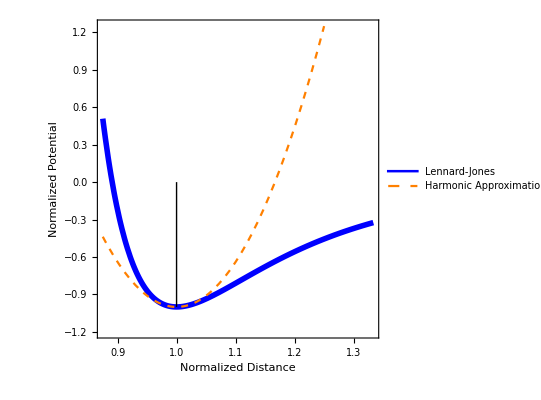

```mathematica
Plot[
{lennardJonesPotentialNonDimensional[ρ],harmonicPotential[ρ]},{ρ,7/8,4/3},

]
```

To make the connection with what we saw last week with masses and springs more apparent, we can write this as

```mathematica
Normal[Series[lennardJonesPotentialEminRMin[r],{r,rMin,2}]]
```

-eMin+(36 eMin (r-rMin)^2)/rMin^2

where we’ve defined the spring constant

Let’s start by considering a finite lattice of  atoms

Additionally, we’ll impose that the first and last atoms are fixed

Our total kinetic energy is simply:

where  and  since we’re fixing the first and last atoms

If we only consider first-nearest neighbor interactions, then each atom is attached to two springs

and the total potential energy is given by:

where  and  since we’re fixing the first and last atoms

We use Hamilton’s equations to proceed further:

Which are particularly simple when we introduce the following non-dimensional parameters:

where  is a non-dimensional velocity
and  is the spring’s characteristic frequency

Let’s write a function to compute the RHS of the second equation (i.e. our normalized forces)

Notice we did not include the first and last positions (since those are fixed, and thus 2 fewer degrees of freedom)

```mathematica
harmonicForces[positions_?ArrayQ, {xleft_, xright_}]:= 
Module[{allpositions = Join[{xleft},positions,{xright}]},
Table[allpositions[[i-1]] + allpositions[[i+1]]-2 allpositions[[i]] ,
{i,2,Length[allpositions]-1}
]
]
```

And solve the system for

```mathematica
domainLength=32;
initialEquilibriumPositions = Range[1,domainLength-1];
initialPositions =initialEquilibriumPositions+.5Sin[ 2((2 Pi initialEquilibriumPositions)/domainLength)];
initialMomenta = ConstantArray[0,Length[initialEquilibriumPositions]];
```

Let’s write a visualization function to visualize our initial conditions

```mathematica
drawAtoms[positions_, {xLeft_, xRight_},originalPositions_]:= Graphics[
{
{Gray,Opacity[1/2],(Disk[{#1,0},1/2]&)/@positions},
{Black,Disk[{xLeft,0},1/2],Disk[{xRight,0},1/2]}
}, ImageSize->300
]
```

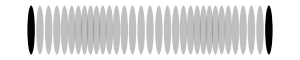

```mathematica
drawAtoms[initialPositions,{0,domainLength},initialEquilibriumPositions]
```

Finally, we solve Hamilton’s two equations

```mathematica
{xSols,pSols}=NDSolveValue[
{
momenta'[t]==harmonicForces[positions[t],{0,32}], 
positions'[t] == momenta[t],
momenta[0] == initialMomenta,
positions[0]==initialPositions
},
{positions,momenta},
{t,0,20},];
```

and animate our solution

```mathematica
Animate[
drawAtoms[xSols[τ],{0,32},initialEquilibriumPositions],
{τ,0,20},AnimationRunning->False,Paneled->False
]
```

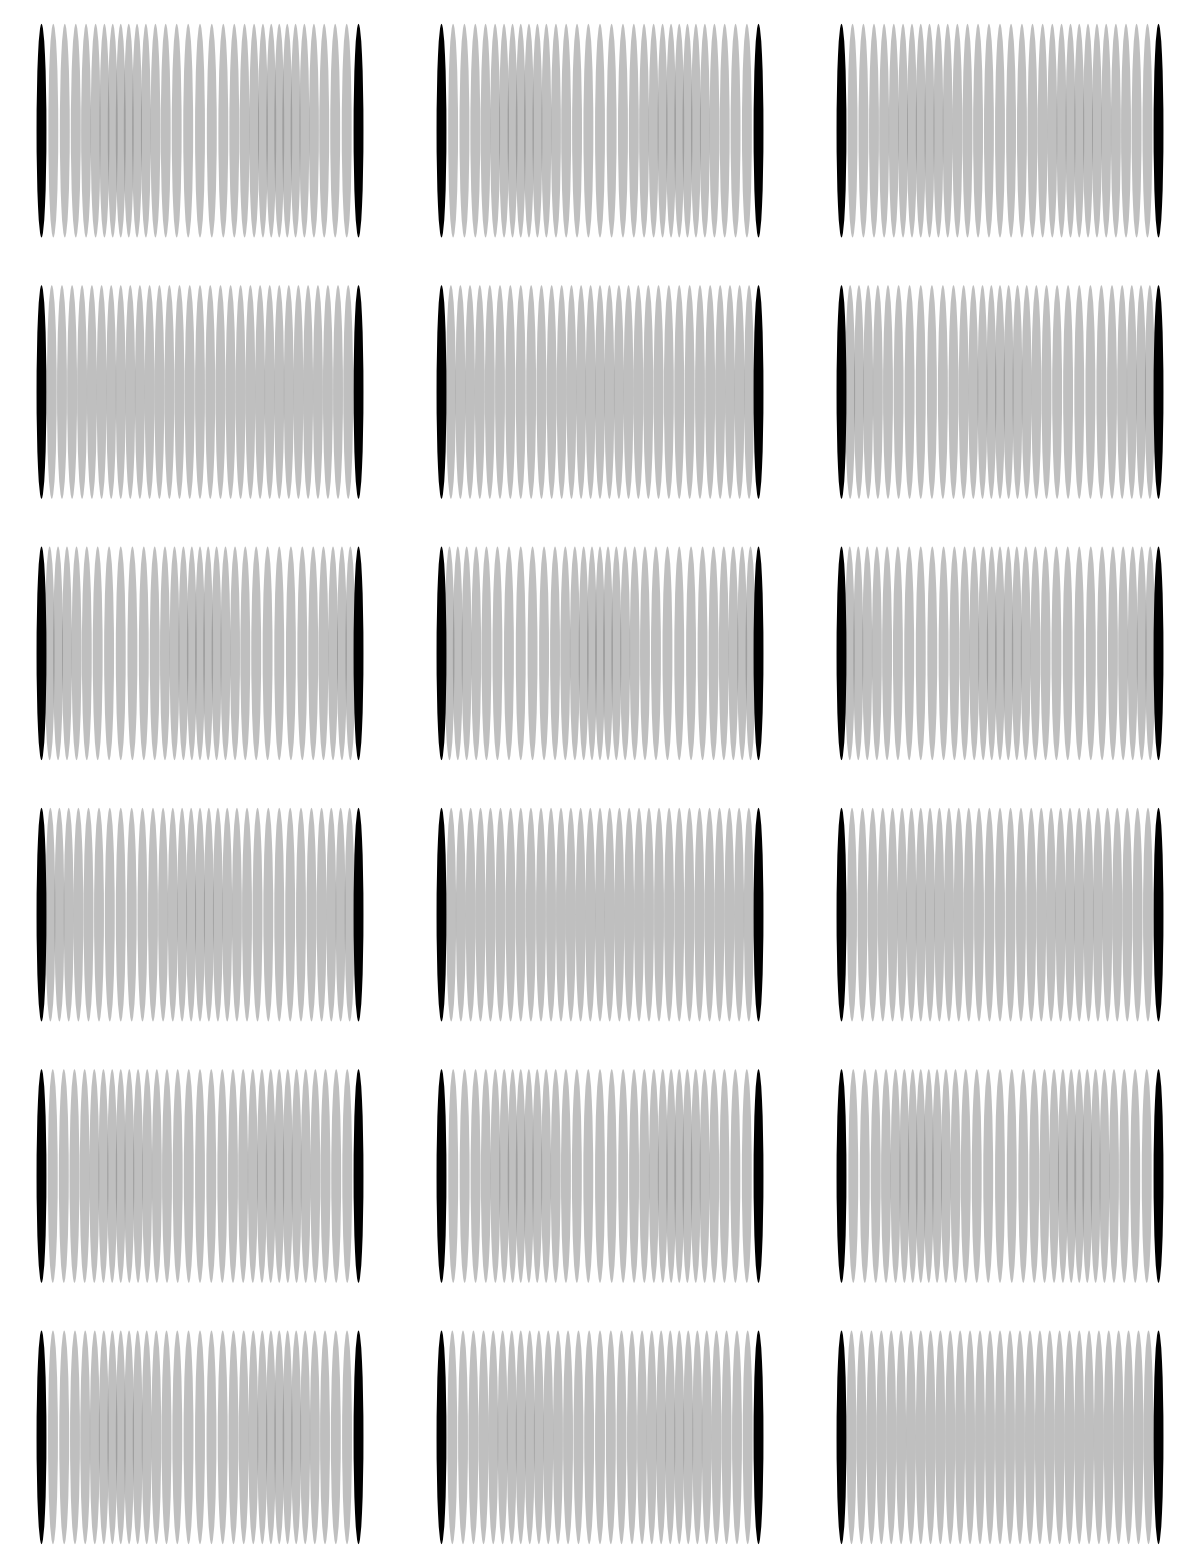

```mathematica
Multicolumn[Table[drawAtoms[xSols[τ],{0,32},initialEquilibriumPositions],{τ,Subdivide[0,20,17]}],3,Appearance->"Horizontal",Frame->All]
```

The visualization with horizontal displacements is hard to see, let’s modify our visualization function to make the oscillations to appear to be vertical
(even though the physics is still horizontal oscillation).

```mathematica
drawAtomsVertical[positions_, {xLeft_, xRight_}, originalPositions_]:=
 Graphics[
{
{Gray,Opacity[1/2],MapThread[Disk[{#1,#2-#1},1/2]&,{originalPositions,positions}]},
{Black,Disk[{xLeft,0},1/2],Disk[{xRight,0},1/2]}
}, ImageSize->300,PlotRange->{-1,1}
]
```

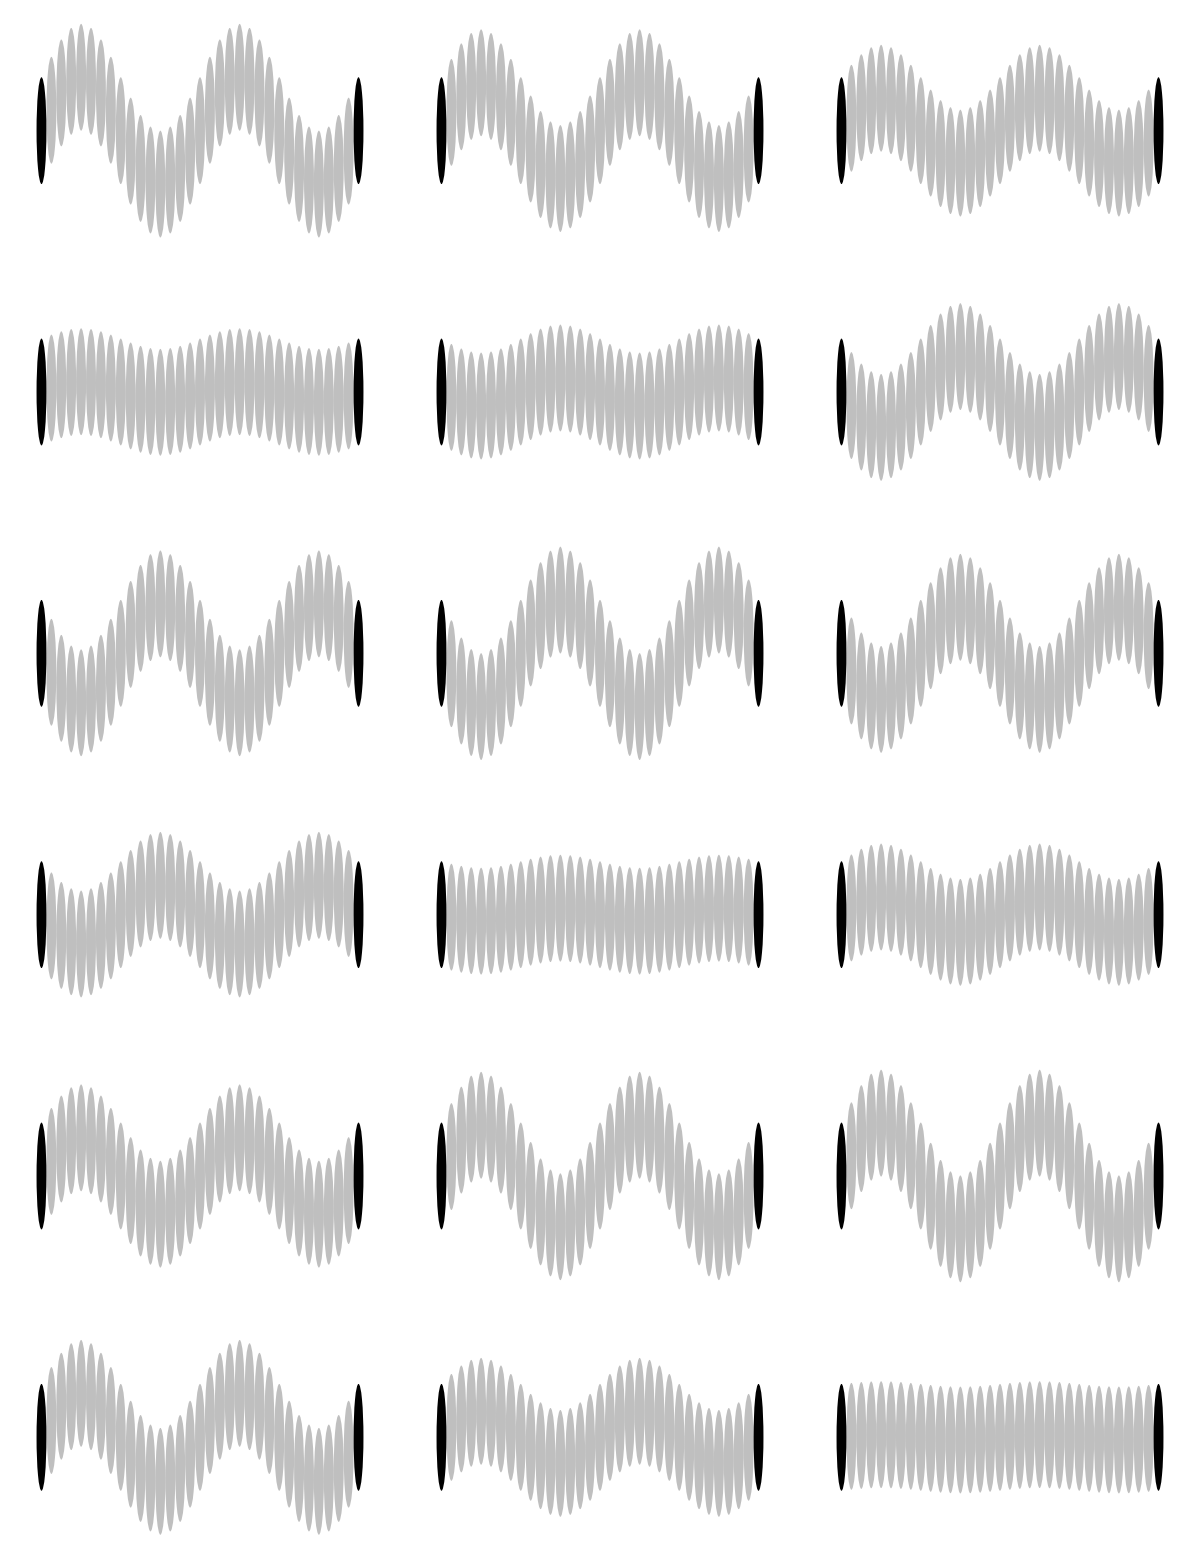

```mathematica
Multicolumn[Table[drawAtomsVertical[xSols[τ],{0,32},initialEquilibriumPositions],{τ,Subdivide[0,20,17]}],3,Appearance->"Horizontal",Frame->All]
```

```mathematica
showVibrationSimulation[positions_,initialPositions_,period_, domainLength_]:= Manipulate[
motion[positions[τ],{0,domainLength},initialPositions],
{τ,0,period},
{motion,{drawAtomsVertical->"Up-Down",drawAtoms->"Left-Right"}},Paneled->False
]
```

```mathematica
showVibrationSimulation[xSols,initialEquilibriumPositions,20,32]
```

### Dispersion Relation

We would like to investigate the oscillation frequency as a function of the initial wavelength within the periodic domain.

To do this, we will ask the solver (NDSolveValue) to stop when the atoms have reached their initial positions again. 
We can query the solutions for the time that solution stopped.

```mathematica
domainLength=32;
initialEquilibriumPositions = Range[1,domainLength-1];
initialPositions =initialEquilibriumPositions+.5Sin[ 5((2 Pi initialEquilibriumPositions)/domainLength)];
initialMomenta = ConstantArray[0,Length[initialEquilibriumPositions]];
```

```mathematica
{xSols,pSols}=NDSolveValue[
{
momenta'[t]==harmonicForces[positions[t],{0,domainLength}], 
positions'[t] == momenta[t],
momenta[0] == initialMomenta,
positions[0]==initialPositions,
WhenEvent[Total[(positions[t]- initialPositions)^2] <10^-8 &&t>0,"StopIntegration",
"DetectionMethod"-> "Interpolation","LocationMethod"->"LinearInterpolation"]
},
{positions,momenta},
{t,0,200},Method->{"SymplecticPartitionedRungeKutta","DifferenceOrder"->2,"PositionVariables"->{positions[t]}},StartingStepSize->1/48,MaxSteps->∞];
```

To do this query, we have to load some functions that Mathematica maintains, but doesn’t load when the program starts.  
The following will load a function that let’s use query the numerical solution’s time domain.

```mathematica
Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"];
```

```mathematica
InterpolatingFunctionDomain[xSols]
```

{{0.,6.66442}}

Let’s check visually be ensuring we only perform one cycle

```mathematica
period = Last[Last[InterpolatingFunctionDomain[xSols]]];
showVibrationSimulation[xSols,initialEquilibriumPositions,period,domainLength]
```

We will write a function to compute the period as described above. Our function will take a domain length and a mode, and return the period, time-dependent positions, and time-dependent momenta as a list.

```mathematica
getHarmonicVibrationSolution[domainLength_, mode_]:=getHarmonicVibrationSolution[domainLength, mode]=
Module[{initialEquilibriumPositions,initialPositions,initialMomenta,xSols,pSols,momenta,positions,period},

initialEquilibriumPositions=Range[1,domainLength-1];
initialPositions =initialEquilibriumPositions+.5 Sin[ mode((2 Pi initialEquilibriumPositions)/domainLength)];
initialMomenta = ConstantArray[0,Length[initialEquilibriumPositions]];

{xSols,pSols}=NDSolveValue[
{
momenta'[t]==harmonicForces[positions[t],{0,domainLength}], 
positions'[t] == momenta[t],
momenta[0] == initialMomenta,
positions[0]==initialPositions,

WhenEvent[Total[(positions[t]-initialPositions)^2]<1/10^8&&t>0,"StopIntegration","DetectionMethod"->"Interpolation","LocationMethod"->"LinearInterpolation"]

},
{positions,momenta},
{t,0,200},];

period =Last[Last[InterpolatingFunctionDomain[xSols]]];

<|"Domain"-> domainLength,"Period"-> period,"Mode"-> mode,
"Positions"-> xSols, "Momenta"-> pSols|>
]
```

For example, for the 24^th mode in a finite lattice of

```mathematica
getHarmonicVibrationSolution[32,24]
```

<|Domain→32,Period→4.4658,Mode→24,Positions→InterpolatingFunction[…],Momenta→InterpolatingFunction[…]|>

We can compute all the solutions for different modes, and extract the angular frequency for each mode.  
It is traditional to plot as a function of the wavenumber k = (2π)/λ_vib= (2π mode)/(domainsize a) ,(i.e., λ_vib =  (domainsize a)/mode).  Our lattice constant here is a = 1.

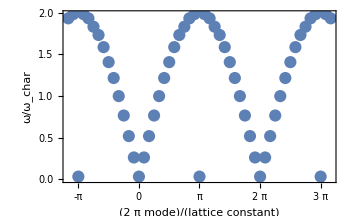

```mathematica
modesAndOmegas24=Table[{(2 π mode)/24,(2 π)/(getHarmonicVibrationSolution[24,mode]["Period"])},{mode,-14,38}];
kPlot =ListPlot[modesAndOmegas24,
Frame->True,FrameLabel->{"(2  π mode)/(lattice constant)","ω/ω_char"},ImageSize->350,BaseStyle->{FontSize->14,PointSize[0.025]},FrameTicks->{{Automatic,None},{{-π,0,π,2 π,3 π},None}}]
```

The behavior is periodic  in the domain (-π/(lattice constant), π/(lattice constant)), or equivalently in (-g/2, g/2) where g is the reciprocal lattice vector.

The periodic domain in reciprocal space is called the first Brillouin zone.

### Enforcing Periodicity on an Infinite Lattice

It’s easy to see by inspection that the solutions look something like

where the  amplitudes q_i^0 are spatially periodic functions of positions with wavelength λ_vibration= (2 π)/k where k is a reciprocal lattice vector.

We can either guess that the continuous solution looks like

Or, we can think of multiplying by the spatially periodic function  as a way of “forcing” the solution to have a specific spatial periodicity.

This idea of forcing periodicity by multiplying by a periodic function will arise frequently in your materials science studies. 
These forcing functions are called Bloch waves and you will see them again in 3.033.

Let’s use our ansatz to the equation for the force we computed above:

```mathematica
forceAnsatz =Simplify[(72 eMin)/rMin^2 q0 Sin[ω t] (Sin[k (j-1)] + Sin[k(j+1)] - 2 Sin[k j])]
```

(144 eMin q0 (-1+Cos[k]) Sin[j k] Sin[t ω])/rMin^2

Using Newton’s equation,

```mathematica
Simplify[
forceAnsatz-mass D[q0 Sin[k j] Sin[ω t],{t,2}] 
]
```

(q0 (-144 eMin+mass rMin^2 ω^2+144 eMin Cos[k]) Sin[j k] Sin[t ω])/rMin^2

Since this must vanish for each atom position

the term in the parenthesis must be zero

Finally, we can use our value of   
and introduce a dimensionless angular frequency,

```mathematica
frequencySols =Solve[Simplify[-144 eMin+mass rMin^2 ω^2+144 eMin Cos[k]/.ω-> √((72 eMin)/(rMin^2 mass)) Ω]==0,Ω]
frequency = Ω/.frequencySols[[2]]
```

{{Ω→-√2 √(1-Cos[k])},{Ω→√2 √(1-Cos[k])}}

√2 √(1-Cos[k])

This is indeed the same solution we obtained by solving the coupled ordinary differential equations numerically.

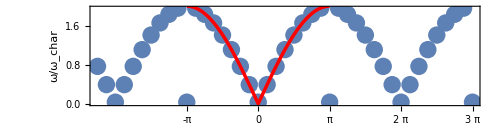

```mathematica
Show[ListPlot[Table[{1/16 (2 π) mode,(2 π)/(getHarmonicVibrationSolution[16,mode]["Period"])},{mode,-18,24}],Frame->True,FrameLabel->{"(2  π mode)/(lattice constant)","ω/ω_char"},ImageSize->500,BaseStyle->{FontSize->14,PointSize[0.025]},FrameTicks->{{Automatic,None},{{-π,0,π,2 π,3 π},None}},AspectRatio->1/4],Plot[frequency,{k,-Pi,Pi}, PlotStyle->Directive[Red,Thickness[0.005]]]]
```

## Infinite Lattice

I find the above exposition, starting from a finite lattice - and then introducing periodicity, to be an intuitive introduction to lattice dynamics

What follows is the more “standard” treatment you will see in 3.033

It starts by specifying the Hamiltonian

```mathematica
hamiltonian["monoatomic"]=Subscript[p, j]^2/(2M)+κ/2(Subscript[u, j]-Subscript[u, j-1])^2+κ/2(Subscript[u, j+1]-Subscript[u, j])^2;
```

And then using Hamilton’s equations to obtain the equations of motion

```mathematica
forceDividedByMass["monoatomic"]=Simplify[-D[hamiltonian["monoatomic"],Subscript[u, j]]/M];

TraditionalForm[
Subscript[u, j]''[t]==forceDividedByMass["monoatomic"]
]
```

u_j''(t)==(κ (u_(j-1)-2 u_j+u_(j+1)))/M

To proceed further, we make the same educated guess on the kind of periodic solutions we expect to get.

Substituting our ansatz in the equation of motion above

Notice that the term in the parenthesis is similar to discrete differentiation

```mathematica
central[function_,order_,index_,shift_:1]:=Sum[(-1)^iter Binomial[order,iter]function[index+(order/2-iter)shift],{iter,0,order}]
```

```mathematica
Limit[central[f,2,i,h],h->0]//TraditionalForm
```

(f(i-h)+f(h+i)-2 f(i))h0

Dividing with ⅇ^ⅈωt we recover another oscillatory equation - this time in space!

This finally motivates us in choosing a single ansatz, exhibiting oscillatory behavior in both space  and time:

```mathematica
ansantz["monoatomic"][j_]:=Simplify[u Exp[ⅈ (j k a-ω t)]]
```

Where we note that shifting our solution by one unit cell, results in us picking up a phase-factor

```mathematica
Simplify[ansantz["monoatomic"][j+1]/ansantz["monoatomic"][j]]
```

ⅇ^(ⅈ a k)

We can now solve the equation of motion for ω^2

```mathematica
equation["monoatomic"]=Simplify[((forceDividedByMass["monoatomic"]/.Subscript[u, index_]:>ansantz["monoatomic"][index])-D[ansantz["monoatomic"][j],{t,2}])/Exp[ⅈ (j k a-ω t)]]
```

(ⅇ^(-ⅈ a k) u ((-1+ⅇ^(ⅈ a k))^2 κ+ⅇ^(ⅈ a k) M ω^2))/M

```mathematica
solution["monoatomic"]=Solve[(equation["monoatomic"]/.ω^2->ωSq)==0,ωSq][[1,1]];
frequencySquared["monoatomic"]=ωSq/.Simplify[ExpToTrig[Expand[solution["monoatomic"]]]];
TraditionalForm[ω^2==frequencySquared["monoatomic"]]
```

ω^2==-(2 κ (cos(a k)-1))/M

Using our non-dimensionalized variables, we obtain the solution as above

```mathematica
Solve[ω^2==frequencySquared["monoatomic"]//.{κ->ωChar^2 M,ωChar->ω/Ω,a->1},Ω]
```

{{Ω→-√2 √(1-Cos[k])},{Ω→√2 √(1-Cos[k])}}

Let’s go further and visualize some of these modes

```mathematica
normalizedFrequency[k_]=√2 √(1-Cos[k]);
```

```mathematica
dispersionGraphic=Plot[normalizedFrequency[k],{k,-π,π},PlotStyle->{Blue,Thickness[0.0075]},FrameLabel->{"(2  π mode)/(lattice constant)","ω/ω_char"},ImageSize->350,FrameTicks->{{Automatic,None},{{{-π,"-g"},0,{π,"g"}},None}},BaseStyle->16,Frame->True,FrameStyle->Thick,AspectRatio->1/(√2)];
```

```mathematica
vibratingAtoms[vamp_,k_, ω_, t_]:=
Table[{1/2+s/2 + Re[(vamp Exp[ⅈ ω t])*Exp[ⅈ s k]], 0}, 
       {s, 10}]
```

Static Visualizations

```mathematica
staticVisualization[vamp_,k_, ω_, t_]:=Column[{
Show[dispersionGraphic,Graphics[Disk[{k,ω[k]},Offset[7.5]]]],
Graphics[GraphicsComplex[vibratingAtoms[vamp,k, ω[k], t],{Red,Disk[#,.125]&/@Range[10]}],PlotRange-> {{0,6},{-.5,.5}},ImageSize->350]}]
```

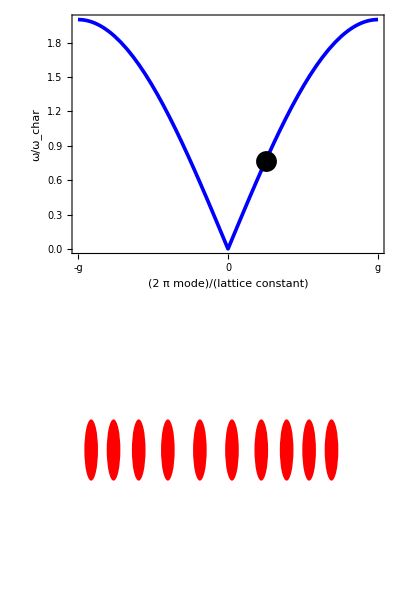

```mathematica
staticVisualization[0.125,π/4,normalizedFrequency,1]
```

Dynamic Visualizations

```mathematica
Manipulate[
DynamicModule[{ω,graphicVib},
Column[
{
graphicVib =  GraphicsComplex[vibratingAtoms[.125,kval,ωval,time],{Red,Disk[#,.125]&/@Range[10]}];

LocatorPane[Dynamic[{kpoint,ω=normalizedFrequency[ kpoint]},(kpoint=First[#1])&],dispersionGraphic,Appearance->Graphics[Disk[],ImageSize->15]],

Animate[Graphics[graphicVib/.{kval-> kpoint, ωval-> ω,time->motiontime},PlotRange-> {{0,6},{-.5,.5}}],{{motiontime,0,"time"},0,4π},Paneled->False,AnimationRunning->False]
}
,Center]
],
{{kpoint,1.5},ControlType->None},Paneled->False]
```